```mathematica
c1[a_][t_] := { t, a Cosh[t/a]}
```

```mathematica
CalculateVectorLength[v_] := FullSimplify[Sqrt[v.v]]
```

```mathematica
CalculateTangentVector[curve_][t_] := Module[{ A=D[curve[tt],tt]}, FullSimplify[A / CalculateVectorLength[A]]] /. tt -> t
CalculateBinormalVector[curve_][t_] := Module[{ A=Cross[D[curve[tt], tt], D[curve[tt], { tt, 2 }]] }, FullSimplify[A / CalculateVectorLength[A]]] /. tt->t
RotateVectorInPlane[{p1_,p2_}]:={-p2,p1}
RotateVectorInPlane[{ p1_, p2_,p3_}] := { -p2, p1,p3 }
CalculateNormalVector[curve_][t_] := RotateVectorInPlane[CalculateTangentVector[curve][t]]
```

```mathematica
Print["T = ", CalculateTangentVector[c1[a]][t]]
Print["N = ", CalculateNormalVector[c1[a]][t]]
```

T = {1/(√(Cosh[t/a]^2)),Sinh[t/a]/(√(Cosh[t/a]^2))}

N = {-Sinh[t/a]/(√(Cosh[t/a]^2)),1/(√(Cosh[t/a]^2))}

```mathematica
CalculatePlaneCurvature[curve_][t_] := Module[{ A = D[curve[tt],{tt, 2}], B = D[curve[tt], tt]}, FullSimplify[A . RotateVectorInPlane[B] / CalculateVectorLength[B]^3]] /. tt -> t
Print["K = ", CalculatePlaneCurvature[c1[a]][t]]
```

K = Cosh[t/a]/(a (Cosh[t/a]^2)^(3/2))

```mathematica
CalculateEvolute[curve_][t_] := FullSimplify[curve[t] + (CalculateNormalVector[curve][t] / CalculatePlaneCurvature[curve][t])]
Evolute = CalculateEvolute[c1[a]][t];
Print["Evolute = ", Evolute]
```

Evolute = {t-1/2 a Sinh[(2 t)/a],2 a Cosh[t/a]}

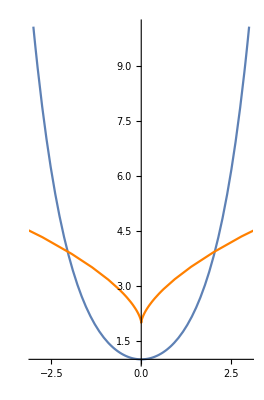

```mathematica
Curve1Plot = ParametricPlot[c1[1][t], {t,-3,3}];
Evolute1Plot = ParametricPlot[Evolute /. a->1, {t,-3,3}, PlotStyle-> Orange];
Show[Curve1Plot, Evolute1Plot]
```

```mathematica
GenerateVectorGraphics[curve_][t_] := Graphics[{
	PointSize[0.02], Point[curve[t]],
	Thick,Blue,Arrow[{curve[t], curve[t]+CalculateTangentVector[curve][t]}],
	Thick,Red,Arrow[{curve[t],curve[t]+CalculateNormalVector[curve][t]}]}];
Animate[Show[Curve1Plot, GenerateVectorGraphics[c1[1]][t]],{t,-3,3}]
```

```mathematica
c2[a_][t_]:={Cos[t],Sin[t],-a*t}/Sqrt[1+a^2t^2]
Curve2Plot=ParametricPlot3D[c2[1][t],{t,-5,5}]
```

-Graphics3D-

```mathematica
CalculateTangentLine[curve_][length_, t_]:=FullSimplify[Line[{curve[tt],curve[tt]+length*CalculateTangentVector[curve][tt]}]]/.tt->t
CalculateNormalLine[curve_][length_,t_]:=FullSimplify[Line[{curve[tt],curve[tt]+length*CalculateNormalVector[curve][tt]}]]/.tt->t
```

```mathematica
Print["Tangent Line = ", CalculateTangentLine[c2[a]][l,t]]
Print["Normal Line = ", CalculateNormalLine[c2[a]][l,t]]
```

Tangent Line = Line[{{Cos[t]/(√(1+a^2 t^2)),Sin[t]/(√(1+a^2 t^2)),-(a t)/(√(1+a^2 t^2))},{((1+a^2 t^2) Cos[t]-(l (Sin[t]+a^2 t (Cos[t]+t Sin[t])))/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2))))/((1+a^2 t^2)^(3/2)),((1+a^2 t^2) Sin[t]+(l (Cos[t]+a^2 t^2 Cos[t]-a^2 t Sin[t]))/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2))))/((1+a^2 t^2)^(3/2)),(a (-t (1+a^2 t^2)-l/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2)))))/((1+a^2 t^2)^(3/2))}}]

Normal Line = Line[{{Cos[t]/(√(1+a^2 t^2)),Sin[t]/(√(1+a^2 t^2)),-(a t)/(√(1+a^2 t^2))},{((1+a^2 t^2) Cos[t]-(l (Cos[t]+a^2 t^2 Cos[t]-a^2 t Sin[t]))/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2))))/((1+a^2 t^2)^(3/2)),((1+a^2 t^2) Sin[t]-(l (Sin[t]+a^2 t (Cos[t]+t Sin[t])))/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2))))/((1+a^2 t^2)^(3/2)),(a (-t (1+a^2 t^2)-l/(√((1+a^2 (1+t^2))/((1+a^2 t^2)^2)))))/((1+a^2 t^2)^(3/2))}}]

```mathematica
Curve2Point={1,0,0};
Reduce[c2[a][t]==Curve2Point, t]
Print["Tangent Line through P(1, 0, 0) with length 1 = ", CalculateTangentLine[c2[a]][1, 0]]
Print["Normal Line through P(1, 0, 0) with length 1 = ", CalculateNormalLine[c2[a]][1,0]]

Curve2PointGraphic=Graphics3D[{PointSize[0.02], Point[{1,0,0}]}];
Show[Curve2Plot,Curve2PointGraphic, Graphics3D[{Thick, Blue, CalculateTangentLine[c2[1]][3,0], Thick, Red, CalculateNormalLine[c2[1]][3,0]}]]
```

(C[1]∈ℤ&&a==0&&t==2 π C[1])||t==0

Tangent Line through P(1, 0, 0) with length 1 = Line[{{1,0,0},{1,1/(√(1+a^2)),-a/(√(1+a^2))}}]

Normal Line through P(1, 0, 0) with length 1 = Line[{{1,0,0},{1-1/(√(1+a^2)),0,-a/(√(1+a^2))}}]

-Graphics3D-

```mathematica
CalculateOsculatingPlane[curve_][x_, y_][t_]:=Module[{V=CalculateBinormalVector[curve][tt], P=curve[tt]}, FullSimplify[(V.P-V[[1]]*x-V[[2]]*y)/V[[3]]]] /.tt->t
CalculateRectifyingPlane[curve_][x_,y_][t_]:=Module[{V=CalculateNormalVector[curve][tt],P=curve[tt]},FullSimplify[(V.P-V[[1]]*x-V[[2]]*y)/V[[3]]]]/.tt->t
Print["Z of the Osulating Plane = ", CalculateOsculatingPlane[c2[a]][x,y][t]]
Print["Z of the Rectifying Plane = ", CalculateRectifyingPlane[c2[a]][x,y][t]]
```

Z of the Osulating Plane = -(a (t (1+a^2 t^2)^2+√(1+a^2 t^2) ((y+a^2 (y+t (x+t y))) Cos[t]-(x+a^2 (1+t^2) x-a^2 t y) Sin[t])))/(√(1+a^2 t^2) (1+a^4 t^4+a^2 (1+2 t^2)))

Z of the Rectifying Plane = ((1+a^2 (-1+t) t)/(√(1+a^2 t^2))-(x+a^2 t^2 x+a^2 t y) Cos[t]-(y+a^2 t (-x+t y)) Sin[t])/a

```mathematica
Curve2OsculatingPlanePlot=Module[{F=CalculateOsculatingPlane[c2[1]][x,y][0]}, Plot3D[F,{x,-2,2},{y,-2,2}]];
Curve2RectifyingPlanePlot=Module[{F=CalculateRectifyingPlane[c2[1]][x,y][0]},Plot3D[F,{x,-2,2},{y,-2,2}]];
Show[Curve2Plot,Curve2PointGraphic,Curve2OsculatingPlanePlot,Curve2RectifyingPlanePlot]
```

-Graphics3D-